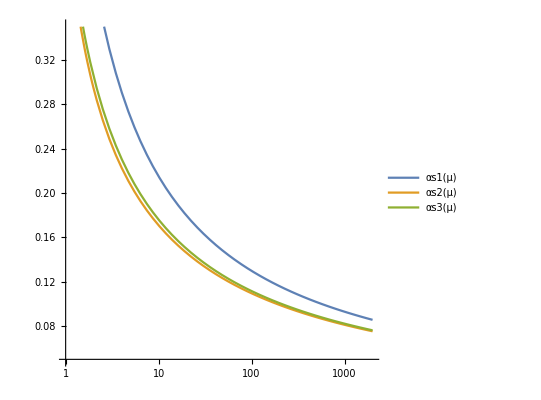

```mathematica
Nc=3;
CA=Nc;
CF=(Nc^2-1)/(2Nc);
TR=1/2;

Nf=4;
Λ=0.3;

b0=(11CA-4Nf TR)/(12π);
b1=(17 CA^2-Nf TR(10CA+6CF))/(24 π^2);
b2=(2857-5033/9 Nf+325/27 Nf^2)/(128 π^3);

αs1[μ_]:=1/(b0 Log[μ^2/Λ^2]);
αs2[μ_]:=1/(b0 Log[μ^2/Λ^2])(1-b1/b0^2 Log[Log[μ^2/Λ^2]]/Log[μ^2/Λ^2]);
αs3[μ_]:=1/(b0 Log[μ^2/Λ^2])(1-b1/b0^2 Log[Log[μ^2/Λ^2]]/Log[μ^2/Λ^2]+(b1^2(Log[Log[μ^2/Λ^2]]^2-Log[Log[μ^2/Λ^2]]-1)+b0 b2)/(b0^4 Log[μ^2/Λ^2]^2));

LogLinearPlot[{αs1[μ],αs2[μ],αs3[μ]},{μ,1,2000},
PlotRange->{0.05,0.35},
PlotLegends->"Expressions",
AspectRatio->1
]
```